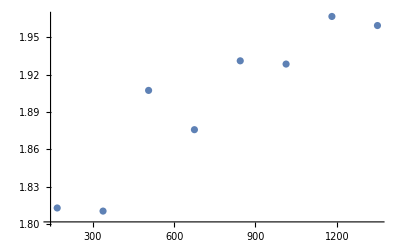
```mathematica
(* This notebook is to be appended to the end of causal_d=3.nb*)

Fitting for Subscript[m, 3]
PointsSample =Select[PointsSample,#[[1]]>1&];
Clear[α]
fit=NonlinearModelFit[PointsSample,α/(2π τ),{α},τ]
Show[Plot[Normal[fit],{τ,0,l},PlotRange->{{0,l},{-1,4}},PlotStyle->Green,PlotLegends->Placed[{"Fit of scatter"},{0.77,.65}]],Plot[{1/(2 π) Cos[m x]/x},{x,0,l},PlotLegends->Placed[{"Analyitic Curve"},{0.75,.75}],PlotStyle->{Red}],ListPlot[PointsSample,PlotLegends->Placed[{"Proper time from longest path"},{0.77,.55}],PlotStyle->{PointSize[0.00001],Blue}],PlotRange->{{0,l},{-1,4}},AxesOrigin->{0,0}]
FittedModel[…]
,
m3
n
fit["ParameterEstimates"]
α:=1.03165
Δα:=fit["EstimatedVariance"]
α
Δα
m3/α
m3*Δα/(α)^2
1.8701503305151406
1000
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"39446.28005067701`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."

1.03165
0.0002718006790384761
1.8127759710319786
0.00047759777043679993
fit["Properties"]
{"AdjustedRSquared","AIC","AICc","ANOVA","BestFit","BestFitParameters","BIC","CorrelationMatrix","CovarianceMatrix","CurvatureConfidenceRegion","Data","Weights","EstimatedVariance","FitCurvature","FitResiduals","Function","HatDiagonal","MaxIntrinsicCurvature","MaxParameterEffectsCurvature","MeanPredictions","MeanPredictionBands","ParameterEstimates","ParameterConfidenceRegion","ParameterBias","PredictedResponse","Properties","Response","RSquared","SingleDeletionVariances","SinglePredictions","SinglePredictionBands","StandardizedResiduals","StudentizedResiduals"}
ListPlot[{{169,1.8128},{338,1.8103},{506,1.9074},{675,1.8758},{844,1.9312},{1013,1.9286},{1182,1.9669},{1350,1.9596}},PlotRange->All]
-Graphics-
```